Рассмотрим интегралы I1 и I2:

```mathematica
I1=Integrate[(1-((1-Sqrt[1-c^2/x^2])/(1+Sqrt[1-c^2/x^2]))^2)*x,{x,c,1}]
```

```mathematica
I1=Expand[Simplify[I1,Assumptions->{0<c<1}]]
```

В матлабовском коде встречается следующее выражение для того же интеграла:

```mathematica
I1m = 1/2 *(c^2 + 1/c^2) - 1 + (1/4)*(1-2/c^2)*Sqrt[1-c^2]-(c^2/8)*Log[c^2/(2-c^2+2*Sqrt[1-c^2])]
```

На графике видно, что кто-то очень неправ

```mathematica
Plot[{I1, I1m},{c,0,1}]
```

Теперь второй интеграл

```mathematica
I2=Integrate[(1-((1-Sqrt[1-c^2/x^2])/(1+Sqrt[1-c^2/x^2]))^2)*x^2,{x,c,1}]
```

```mathematica
I2=Expand[Simplify[I2,Assumptions->{0<c<1}]]
```

```mathematica
I2m = (2/3)*(1-c^3)+(2/3)*(1-c^2)^(3/2)-(2/(5*c^2))*(1-c^5)+(2/(5*c^2))*(1-c^2)^(5/2)
```

```mathematica
Plot[{I2,I2m},{c,0,1}]
```

Здесь уже больше похоже на правду

Теперь займёмся решением задачи. Для этого нам нужны следующие величины:

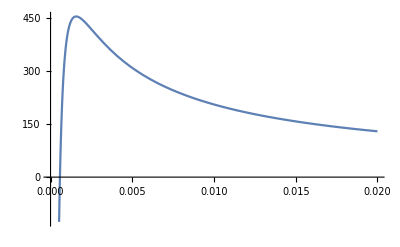

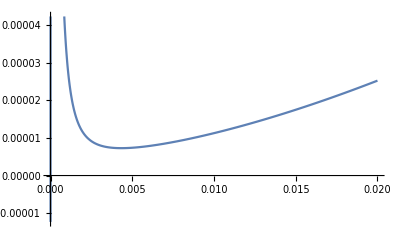

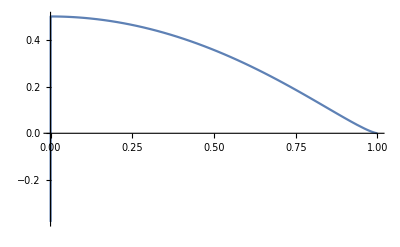

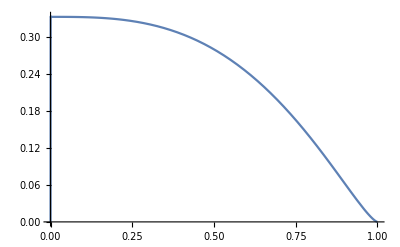

-Graphics3D-

```mathematica
Subscript[E, e] = 511003.4;
Subscript[r, e]=2.8179403267*10^-13;
Subscript[N, a] =6.0221413*10^23;
α = 0.00729735256;
ρ= 5.3500;
Z = 32;
M=72.600;
Subscript[U, 0]=12.5;
J = Piecewise[{{13.6Z ,Z < 10},{(9.76 + 58.8 Z^-1.19)Z ,Z ≥ 10}}]/Subscript[E, e] ;
Delta[x_]:=HeavisidePi[1000*x];(*тупая идея, но с обычной функцией Дирака не работает*)
f[T_]:=0.12Delta[T-7.9*10^3/Subscript[E, e]] + 0.88Delta[T-6.83*10^3/Subscript[E, e]]+0.86Delta[T-1.16*10^3/Subscript[E, e]];
η[T_]:=1/4((α Z^(1/3))/0.885)^2 1/(T(T+2))(1.13+3.76 α^2 Z^2(T+1)^2/(T(T+2)));

ϵ [T_]:=  (2 π ρ Subscript[N, a] Z)/M((T+1)^2 Subscript[r, e]^2)/(T(T+2))(2Log[1.166T/J]);
Subscript[λ, tr][T_]:=((2 π ρ Subscript[N, a] Z(Z+1))/M((T+1)^2 Subscript[r, e]^2)/(T^2(T+2)^2)(Log[1+1/η[T]]-1/(η[T]+1)))^-1;
Subscript[I, 1][t_]:=-4/(3 t^4)+2/t^2-(2 t^2)/3+(4 √(1-t^2))/(3 t^4)-(4 √(1-t^2))/(3 t^2);
Subscript[I, 2][t_]:=-8/(7 t^4)+8/(5 t^2)-(16 t^3)/35-(4 √(1-t^2))/105+(8 √(1-t^2))/(7 t^4)-(36 √(1-t^2))/(35 t^2)-8/105 t^2 √(1-t^2);
Plot[ϵ[T],{T, 0, 0.02}]
Plot[Subscript[λ, tr][T],{T, 0, 0.02}]
Plot[Subscript[I, 1][t],{t, 0,1}]
Plot[Subscript[I, 2][t],{t, 0,1}]
(*ещё разок стоит проверить уравнения, потому как решение выглядит странно*)
eq=D[u[x,T], T]==(-Subscript[λ, tr][T])/(3ϵ[T])D[u[x,T], x,x] -f[T];
bc={u[x,0.02]==0,Derivative[1,0][u][0,T]-(3 Subscript[I, 1][Subscript[U, 0]/T])/((2-3 Subscript[I, 2][Subscript[U, 0]/T])Subscript[λ, tr][T])u[0,T]==0,u[1,T]==0};
soln=NDSolve[{eq, bc}, u,{T,0.02,0.005},{x,0,1}];
Plot3D[u[x,T]/.soln,{x,0,1},{T,0.005,0.02},PlotRange->All]
```